## Phase plots of autonomous linear differential equations

## Math 4354 Prof. Katharine Long

The function below plots a vector field showing the system’s motion in the phase plane. Eigenvalues are printed in the plot header. If the eigenvectors are real (which will be the case for real eigenvalues) they are shown as arrows: v_1 in red, v_2 in blue. The colorbar to the right of the plot shows the magnitude of the stream vectors; the lengths of the vectors shown are scaled logarithmically for clarity.

```mathematica
phasePlot[A_]:=Module[{Vt=Eigenvectors[A],v1,v2,lam=Eigenvalues[A]},
v1 = Vt[[1]]/Norm[Vt[[1]]];
v2=Vt[[2]]/Norm[Vt[[2]]];
VectorPlot[A.{x,y},{x,-1,1},{y,-1,1},(*PlotLegends->Automatic,*)VectorScaling->"Log",VectorPoints->20,
(*PlotLabel->StringForm["λ_1=``, λ_2=``", lam[[1]],lam[[2]]],*)
Epilog->If[Im[v1]=={0,0}&& Im[v2]=={0,0},{Red,Arrow[{{0,0},v1}],Blue,Arrow[{{0,0},v2}]},{}]]
]
```

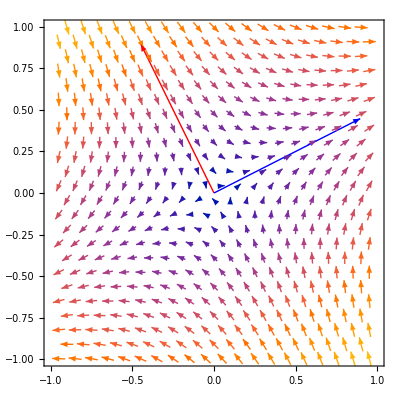

```mathematica
phasePlot[{{1,2},{2,-2}}]
```

## Attractors

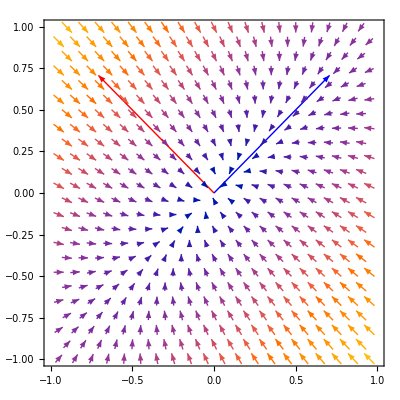

```mathematica
phasePlot[{{-2,1},{1,-2}}]
```

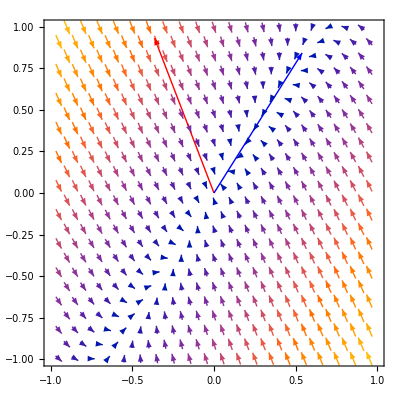

```mathematica
phasePlot[{{-2,1},{4,-3}}]
```

## Repellers

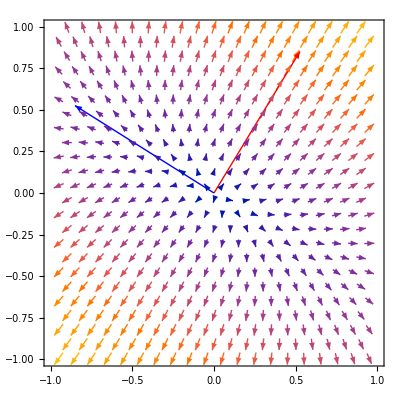

```mathematica
phasePlot[{{2,1},{1,3}}]
```

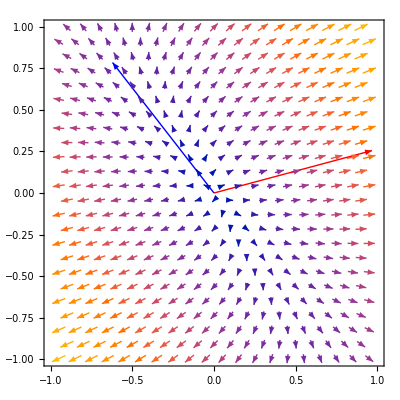

```mathematica
phasePlot[{{2,1},{1/3,1}}]
```

## Saddle points (aka hyperbolic points)

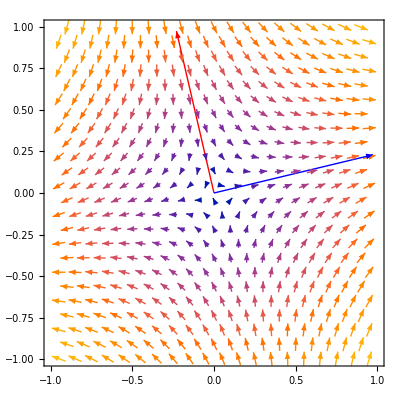

```mathematica
phasePlot[{{2,1},{1,-2}}]
```

```mathematica
V=Transpose[{{-1,5},{2,2}}]
```

(-1 | 2
5 | 2)

```mathematica
Λ = {{2,0},{0,-1}}
```

(2 | 0
0 | -1)

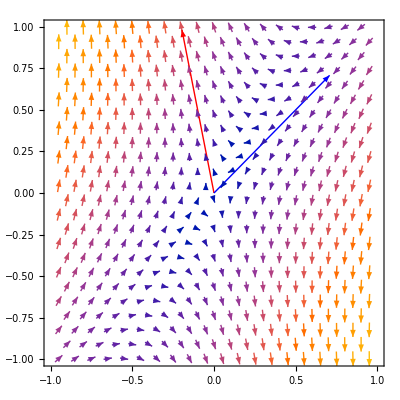

```mathematica
phasePlot[V.Λ.Inverse[V]]
```

## Oscillation

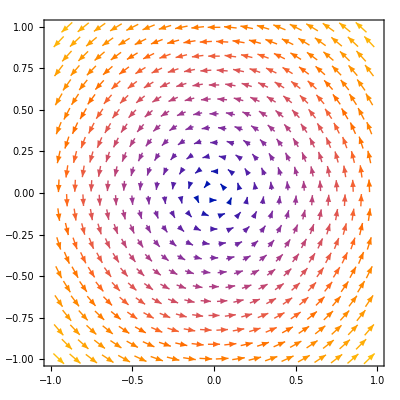

```mathematica
phasePlot[{{0,-1},{1,0}}]
```

## Attractors with oscillation

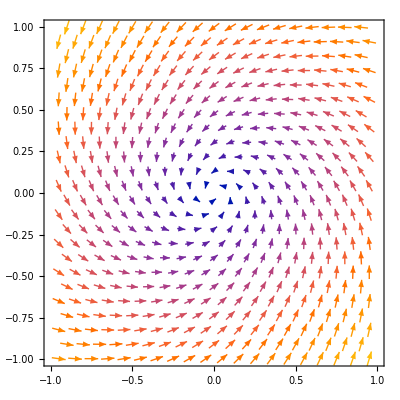

```mathematica
phasePlot[{{-2,-4},{4,-3}}]
```

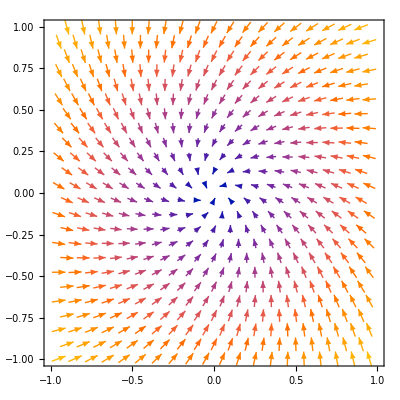

```mathematica
phasePlot[{{-4,-2},{2,-4}}]
```

## Repellors with oscillation

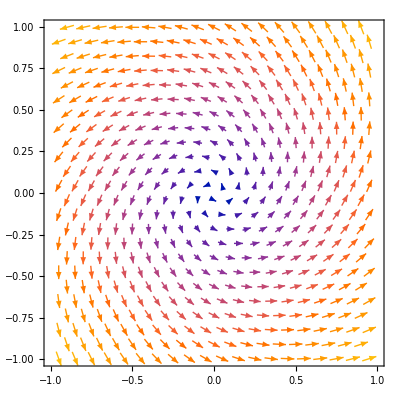

```mathematica
phasePlot[{{2,-4},{4,2}}]
```

If A  is real, can you have a saddle point with oscillation? What would the eigenvalues have to look like?